```mathematica
Clear["Global`*"]
Cel1=2;Cel2=2;Rl1=50;Rl2=50;Cth = 10;k =0.7;
Tc =340;Ts=300;Rins1=100;Rmet1=5;Rins2=95;Rmet2=4.75;steps = 10000;dt=0.5;

V1=Table[0,{i,1,steps}];T1=Table[Ts,{i,1,steps}];
V2=Table[0,{i,1,steps}];T2=Table[Ts,{i,1,steps}];
Current1=Table[0,{i,1,steps}];Current2=Table[0,{i,1,steps}];

a=0.06;
Vapl1=130;
Vapl2=70;
dT=0.01;

P[T_]:=1-1/(1+Exp[(T-Tc)/dT]);
```

```mathematica
Rdevice1=Rins1;
Rdevice2=Rins2;
For[i=1,i<steps,i++,
V1[[i+1]]=V1[[i]]+dt/(Cel1 Rl1)(Vapl1-(1+Rl1/Rdevice1)V1[[i]]);
T1[[i+1]]=T1[[i]]+dt/Cth((V1[[i]])^2/Rdevice1+k(Ts-T1[[i]])+a(T2[[i]]-T1[[i]]));
V2[[i+1]]=V2[[i]]+dt/(Cel2 Rl2)(Vapl2-(1+Rl2/Rdevice2)V2[[i]]);
T2[[i+1]]=T2[[i]]+dt/Cth((V2[[i]])^2/Rdevice2+k(Ts-T2[[i]])+a(T1[[i]]-T2[[i]]));
Current1[[i]]=V1[[i]]/Rdevice1;
Current2[[i]]=V2[[i]]/Rdevice2;
If[T1[[i+1]]>T1[[i]],{If[RandomReal[]<P[T1[[i]]],{Rdevice1=Rmet1}]}];
If[T1[[i+1]]<T1[[i]],{If[RandomReal[]>P[T1[[i]]],{Rdevice1=Rins1}]}];
If[T2[[i+1]]>T2[[i]],{If[RandomReal[]<P[T2[[i]]],{Rdevice2=Rmet2}]}];
If[T2[[i+1]]<T2[[i]],{If[RandomReal[]>P[T2[[i]]],{Rdevice2=Rins2}]}];
]
```

General::munfl: Exp[-4000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3999.98] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

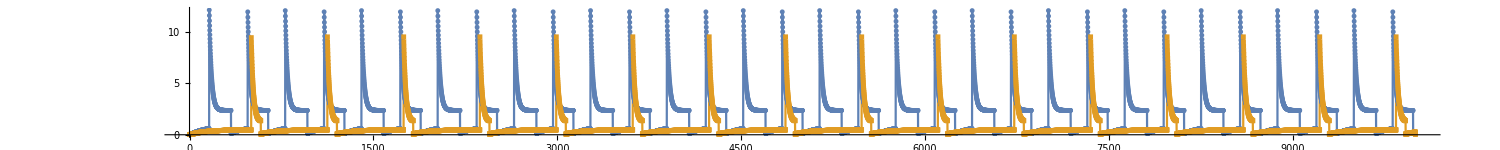

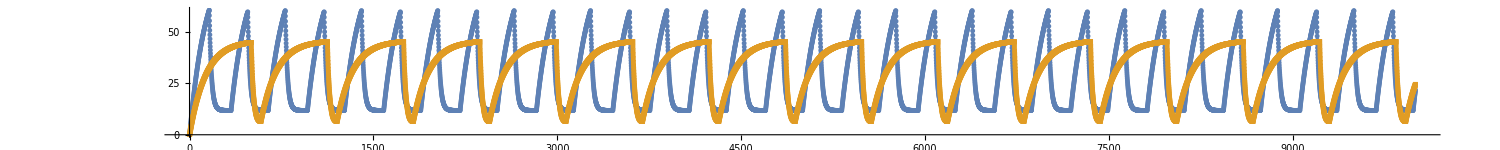

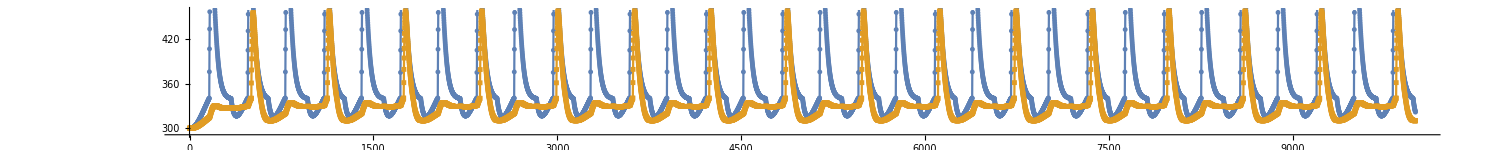

General::munfl: Exp[-3999.8] is too small to represent as a normalized machine number; precision may be lost.

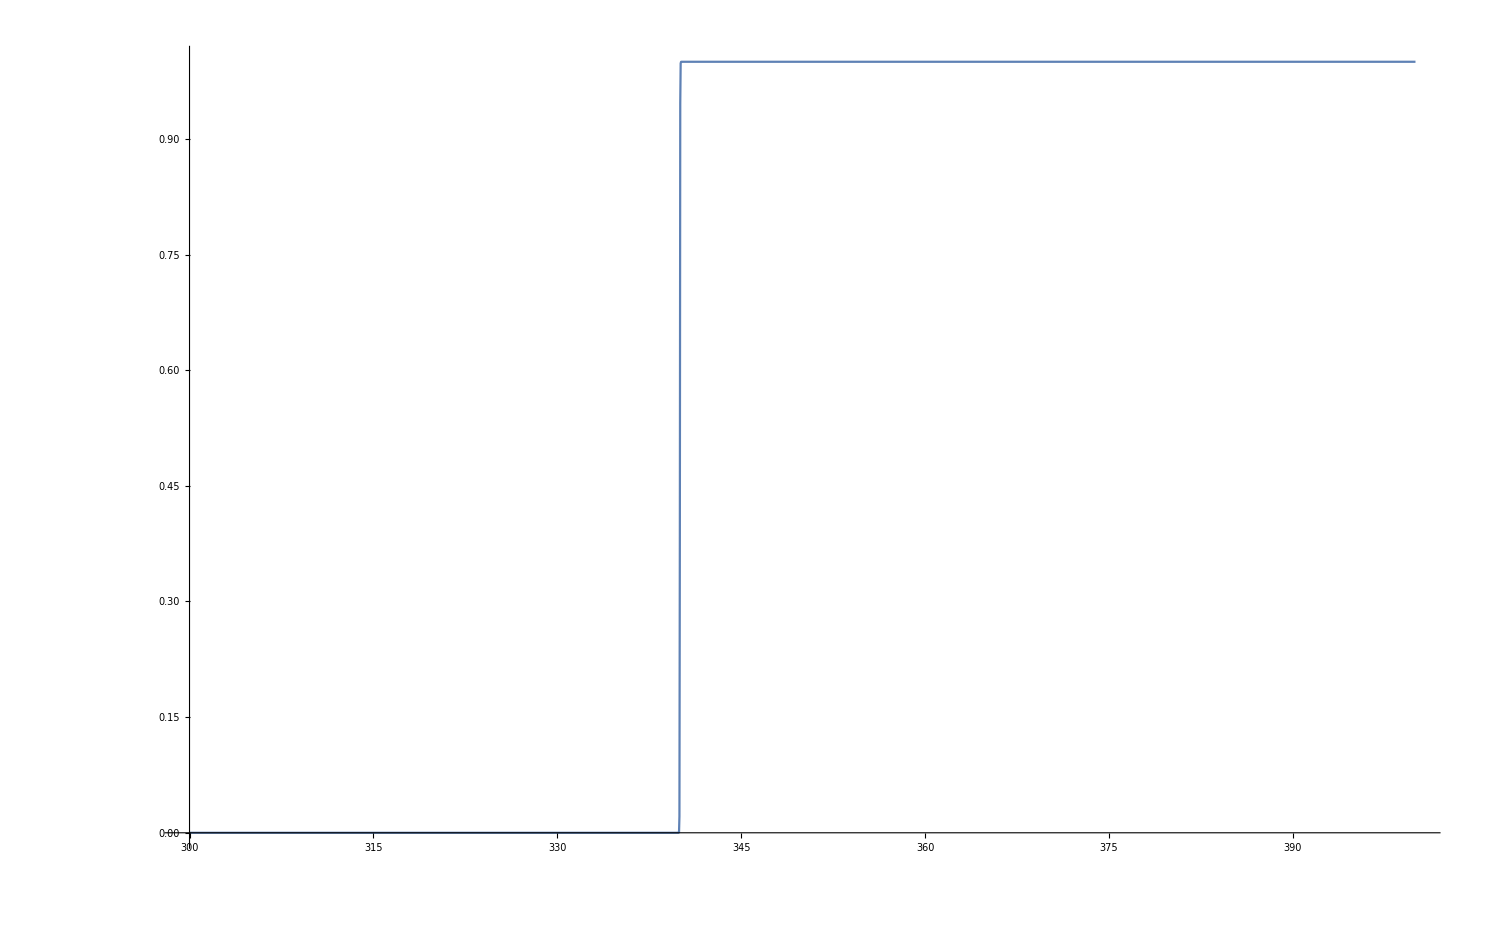

```mathematica
ListPlot[{Current1,Current2},Joined->True,PlotMarkers->{Automatic,5},PlotRange->All,AspectRatio->1/10,ImageSize->1500]
ListPlot[{V1,V2},Joined->True,PlotMarkers->{Automatic,5},AspectRatio->1/10,ImageSize->1500]
ListPlot[{T1,T2},Joined ->True, PlotMarkers->{Automatic,5},AspectRatio->1/10,ImageSize->1500]

Plot[P[T],{T,300,400}]

index=Table[i,{i,1,steps}];
save=Transpose[{index,Current1,Current2,V1,V2,T1,T2}];
Export["C:\\Users\\pavel\\Documents\\OneDrive - University of Denver\\Research\\6 - VO2 thermal coupling model\\Micro-devices\\1-2 mode 70 V.txt",save,"Table"];
```